```mathematica
(*
e[x]_here = e[1][x]_{Lagrangian approach}
*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
ϵ[1]=1;
```

```mathematica
ass={ψ[x]∈Reals,ν[x]>0};
```

```mathematica
e[x_]:=ν[x]{Cos[ψ[x]],-Sin[ψ[x]]}
```

```mathematica
n[x_]:={-e[x][[2]],e[x][[1]]}/Norm[e[x]]
```

```mathematica
g[x_]:=Simplify[{{e[x].e[x]}},Assumptions->ass]
```

```mathematica
sqrtdetg[x_]:=Sqrt[Det[g[x]]]
```

```mathematica
gc[x_]:=Inverse[g[x]]
```

```mathematica
FullSimplify[{{-n'[x].e[x]}},Assumptions->ass]
```

{{-ν[x] ψ'[x]}}

```mathematica
b[x_]:={{-ν[x] ψ'[x]}}
```

```mathematica
1/2FullSimplify[Sum[gc[x][[i,j]]b[x][[j,i]],{i,1,1},{j,1,1}],Assumptions->ass]
```

-ψ'[x]/(2 ν[x])

```mathematica
H[x_]:=-ψ'[x]/(2 ν[x])
```

```mathematica
K[x_]:=0
```

```mathematica
Γ[x_]:=ResourceFunction["ChristoffelSymbol"][g[x],{x}] //FullSimplify
```

```mathematica
Γ[x]
```

{{{ν'[x]/ν[x]}}}

```mathematica
(* \Nabla_k f_i*)
```

```mathematica
Nablaf[f_][i_,k_][x_]:=Derivative[ϵ[k]][f[i]][x]-Sum[f[j][x] Γ[x][[j,i,k]],{j,1,1}]
```

```mathematica
dH[1][x_]:=H'[x]
```

```mathematica
FullSimplify[Sum[gc[x][[i,j]]Nablaf[dH][i,j][x],{i,1,1},{j,1,1}],Assumptions->ass]
```

(-3 ν'[x]^2 ψ'[x]+3 ν[x] ν'[x] ψ''[x]+ν[x] (ψ'[x] ν''[x]-ν[x] ψ^(3)[x]))/(2 ν[x]^5)

```mathematica
NabNabH[x_]:=(-3 ν'[x]^2 ψ'[x]+3 ν[x] ν'[x] ψ''[x]+ν[x] (ψ'[x] ν''[x]-ν[x] Derivative[3][ψ][x]))/(2 ν[x]^5)
```

```mathematica
eqψ=FullSimplify[{2 κ(2H[x](H[x]^2-K[x])+NabNabH[x])-2 σ[x]H[x]==0},Assumptions->ass]
```

{2 ν[x] (ψ'[x] (ν[x]^3 σ[x]+κ ν''[x])+3 κ ν'[x] ψ''[x])==6 κ ν'[x]^2 ψ'[x]+κ ν[x]^2 (ψ'[x]^3+2 ψ^(3)[x])}

```mathematica
eqX={X1'[x]==ν[x] Cos[ψ[x]],X2'[x]==-ν[x] Sin[ψ[x]]}
```

{X1'[x]==Cos[ψ[x]] ν[x],X2'[x]==-Sin[ψ[x]] ν[x]}

```mathematica
bcs={ψ[xmin]==ψmin,ψ[xmax]==ψmax,ψ'[xmin]==ψpmin,X1[xmin]==X1min,X2[xmin]==X2min};
```

```mathematica
σ[x_]:=σc
(*fix the gauge*)
ν[x_]:=1.1 x/(1+x)
```

```mathematica
eqψ
```

{(2.2 x ((((2.2 x)/(1+x)^3-2.2/(1+x)^2) κ+(1.331 x^3 σc)/(1+x)^3) ψ'[x]+3 (-(1.1 x)/(1+x)^2+1.1/(1+x)) κ ψ''[x]))/(1+x)==6 (-(1.1 x)/(1+x)^2+1.1/(1+x))^2 κ ψ'[x]+(1.21 x^2 κ (ψ'[x]^3+2 ψ^(3)[x]))/(1+x)^2}

```mathematica
(*parameters*)
```

```mathematica
κ=1;
σc=1;
xmin=1;
xmax=3;
ψmin=-1/2;
ψmax =2.5;
ψpmin=-2 ν[xmin]*0.5;
X1min=0;
X2min=0;
```

```mathematica
s=NDSolve[Flatten[{eqψ,eqX,bcs}],{ψ,X1,X2},{x,xmin,xmax}]
```

{{ψ→InterpolatingFunction[…],X1→InterpolatingFunction[…],X2→InterpolatingFunction[…]}}

```mathematica
X2[xmax]/.s
```

{-0.28616}

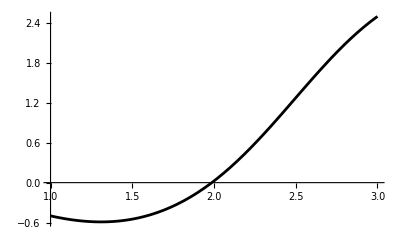

```mathematica
plotψexact=Plot[ψ[x]/.s,{x,xmin,xmax},PlotStyle->Black]
```

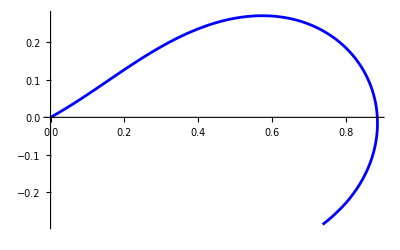

```mathematica
plotXexact=ParametricPlot[{X1[x],X2[x]}/.s,{x,xmin,xmax},PlotStyle->Blue]
```

```mathematica
(*check FE solution*)
```

```mathematica
(*check ψ*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/one_dimension/solution/nodal_values/psi.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

{{3.,2.5},{2.9,2.30645},{2.8,2.08093},{2.7,1.82871},{2.6,1.55701},{2.5,1.27479},{2.4,0.991902},{2.3,0.717997},{2.2,0.46149},{2.1,0.228818},{2.,0.0241998},{1.9,-0.150192},{1.8,-0.293813},{1.7,-0.407265},{1.6,-0.491868},{1.5,-0.549339},{1.4,-0.581595},{1.3,-0.590649},{1.2,-0.578584},{1.1,-0.547586},{1.,-0.5}}

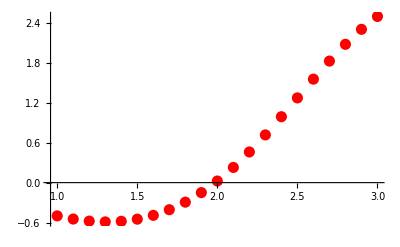

```mathematica
plotψnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

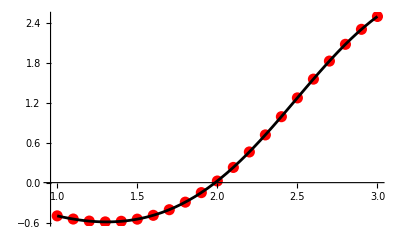

```mathematica
Show[plotψnum,plotψexact]
```

```mathematica
(*check X*)
```

```mathematica
tX=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/one_dimension/solution/nodal_values/X.csv"];
tX=Table[{tX[[i,1]],tX[[i,2]]},{i,2,Length[tX]}]
```

{{0.738179,-0.286843},{0.799073,-0.231815},{0.846729,-0.165917},{0.877108,-0.091329},{0.88698,-0.0122281},{0.87492,0.0656999},{0.841934,0.136336},{0.791381,0.194441},{0.728164,0.236675},{0.65758,0.261959},{0.584302,0.271171},{0.511799,0.266483},{0.44221,0.250661},{0.376527,0.226532},{0.314898,0.196688},{0.256943,0.16336},{0.20202,0.128418},{0.149415,0.0934131},{0.0984868,0.0596449},{0.0487626,0.0282045},{9.23426×10^-35,2.12229×10^-34}}

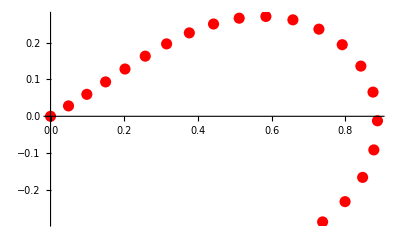

```mathematica
plotXnum=ListPlot[tX,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

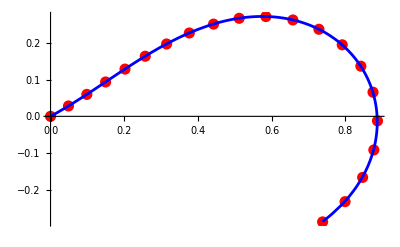

```mathematica
Show[plotXnum,plotXexact,PlotRange->Full]
```

```mathematica
(*plot the normal to the manifold n*)
```

```mathematica
(*tn=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/one_dimension/solution/nodal_values/n.csv"];
tn=Table[{tn[[i,1]],tn[[i,2]]},{i,2,Length[tn]}]*)
```

```mathematica
(*plotn=Graphics[{Red,Table[Arrow[{{tX[[i,1]],tX[[i,2]]},{tX[[i,1]]+0.1*tn[[i,1]],tX[[i,2]]+0.1*tn[[i,2]]}}],{i,1,Length[t]}]},Frame->True,AspectRatio->1,PlotRange->All]*)
```